# ch1Introduction.nb Some basic principles

## Test Cases

### testCase0017: (1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3

#### Expansion at the origin

```mathematica
$theFunction=(1+4 z^2)+(5/2+3/4 z)w^2+(z-3/4 z^2)w^3


aForm[$theFunction]
```

1+w^2 (5/2+(3 z)/4)+4 z^2+w^3 (z-(3 z^2)/4)

(1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3

### Checking f_w(s_i,w_i)=0 for each singular point and some w_i with f(s_i,w_i)=0

```mathematica
res= Resultant[$theFunction,D[$theFunction,w],w];
singList=DeleteDuplicates@NSolveValues[res==0,z];
wVals=NSolveValues[$theFunction==0/.z->singList[[2]],w]
D[$theFunction,w]/.{z->singList[[2]],w->#}&/@ wVals
```

{-0.406393-0.724149 ⅈ,0.812786+1.4483 ⅈ,0.812786+1.4483 ⅈ}

{-1.95584-5.02162 ⅈ,-4.44089×10^-16-8.88178×10^-16 ⅈ,-4.44089×10^-16-8.88178×10^-16 ⅈ}

### testCase0032: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

#### Expansion at the origin

```mathematica
$theFunction=(1+4 z^2)+(5/2+3/4 z)w^2+(z-3/4 z^2)w^3


aForm[$theFunction]
```

1+w^2 (5/2+(3 z)/4)+4 z^2+w^3 (z-(3 z^2)/4)

(1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3

### Checking f_w(s_i,w_i)=0 for each singular point and some w_i with f(s_i,w_i)=0

```mathematica
res= Resultant[$theFunction,D[$theFunction,w],w];
singList=DeleteDuplicates@NSolveValues[res==0,z];
wVals=NSolveValues[$theFunction==0/.z->singList[[2]],w]
D[$theFunction,w]/.{z->singList[[2]],w->#}&/@ wVals
```

{-0.406393-0.724149 ⅈ,0.812786+1.4483 ⅈ,0.812786+1.4483 ⅈ}

{-1.95584-5.02162 ⅈ,-4.44089×10^-16-8.88178×10^-16 ⅈ,-4.44089×10^-16-8.88178×10^-16 ⅈ}

```mathematica
function0032=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7z^3+8z^4)w^4;

Print[Style[aForm[function0032],8]]
```

(function32)

```mathematica
pSeries=w/.AsymptoticSolve[function0032==0,w,{z,0,5}]//N//MatrixForm
```

(-0.25 z+0.0703125 z^2+0.020752 z^3+0.0039978 z^4-0.106094 z^5
(0.-1.41421 ⅈ) √z-2.875 z+(0.+13.3301 ⅈ) z^(3/2)+83.9648 z^2-(0.+611.292 ⅈ) z^(5/2)-4762.51 z^3+(0.+38916.8 ⅈ) z^(7/2)+329091. z^4-(0.+2.85553×10^6 ⅈ) z^(9/2)-2.52802×10^7 z^5
(0.+1.41421 ⅈ) √z-2.875 z-(0.+13.3301 ⅈ) z^(3/2)+83.9648 z^2+(0.+611.292 ⅈ) z^(5/2)-4762.51 z^3-(0.+38916.8 ⅈ) z^(7/2)+329091. z^4+(0.+2.85553×10^6 ⅈ) z^(9/2)-2.52802×10^7 z^5
0.333333+4.66667 z-168.222 z^2+9523.5 z^3-658181. z^4+5.05604×10^7 z^5)

## Section 1.2: Illustrate z^{1/2}

### Use built-in z^{1/2} function

#### Illustrate imaginary sheets

```mathematica
imag1= ParametricPlot3D[{Re@z,Im@z,Im[z^{1/2}]}/.z->r Exp[I t],{r,0,2},{t,-Pi,Pi},PlotStyle->{Opacity[0.3],Blue}];
imag2= ParametricPlot3D[{Re@z,Im@z,-Im[z^{1/2}]}/.z->r Exp[I t],{r,0,2},{t,-Pi,Pi},PlotStyle->{Opacity[0.3],Red}];
Show[{imag1,imag2},PlotRange->All,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["x",14,Bold,Black],Style["y",14,Bold,Black],Style["Im(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted]]
```

-Graphics3D-

Notice in the following code how a contour over the default definition of z^{1/2} starting at z=1 on the blue sheet and encounters the default branch-cut at the negative real axis and abruptly drops down to the lower blue sheet of the branch rather than analyticallly-continuing onto the red sheet.

```mathematica
imagContour=ParametricPlot3D[{Re@z,Im@z,Im[z^(1/2)]}/.z->Exp[I t],{t,0,2 Pi},PlotStyle->Yellow];
Show[{imag1,imag2,imagContour},PlotRange->All,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["x",14,Bold,Black],Style["y",14,Bold,Black],Style["Im(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted]]
```

-Graphics3D-

#### Illustrate real sheets

```mathematica
real1= ParametricPlot3D[{Re@z,Im@z,Re[z^{1/2}]}/.z->r Exp[I t],{r,0,2},{t,-Pi,Pi},PlotStyle->{Opacity[0.3],Blue}];
real2= ParametricPlot3D[{Re@z,Im@z,-Re[z^{1/2}]}/.z->r Exp[I t],{r,0,2},{t,-Pi,Pi},PlotStyle->{Opacity[0.3],Red}];
Show[{real1,real2},PlotRange->All,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["x",14,Bold,Black],Style["y",14,Bold,Black],Style["Im(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted]]
```

-Graphics3D-

The same branch-cut discontinuity is observed over the real sheets

```mathematica
realContour=ParametricPlot3D[{Re@z,Im@z,Re[z^(1/2)]}/.z->Exp[I t],{t,0,2 Pi},PlotStyle->Yellow];
Show[{real1,real2,realContour},PlotRange->All,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["x",14,Bold,Black],Style["y",14,Bold,Black],Style["Im(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted]]
```

-Graphics3D-

#### Illustrate contour over z^{1/2} using default definition of z^{1/2} encounters branch-cut

```mathematica
contour1=ParametricPlot3D[{Re@z,Im@z,Im[z^(1/2)]}/.z->Exp[I t],{t,0,2 Pi},PlotStyle->Yellow];
Show[{b1,b2,contour1},PlotRange->All,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["x",14,Bold,Black],Style["y",14,Bold,Black],Style["Im(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted]]
```

-Graphics3D-

### Use exponential form of z^{1/2}: The same branch-cut discontinuity is observed in the exponential form

```mathematica
squareRoot[z_,k_]:=Abs[z]^(1/2) Exp[I/2(Arg[z]+2 k Pi)];
sReal1=ParametricPlot3D[{Re@z,Im@z,Im[squareRoot[z,0]]}/. z->r Exp[I t],{r,0.001,1},{t,-Pi,Pi},PlotRange->All,PlotStyle->{Opacity[0.25],Red}];
(*Plot sheet 2*)
sReal2=ParametricPlot3D[{Re@z,Im@z,Im[squareRoot[z,1]]}/. z->r Exp[I t],{r,0.001,1},{t,-Pi,Pi},PlotRange->All,PlotStyle->{Opacity[0.25],Blue}];
(*Show plots*)
Show[{sReal1,sReal2},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["x",14,Bold,Black],Style["y",14,Bold,Black],Style["Im(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted]]
```

-Graphics3D-

### Create mIVP of z^{1/2} and contour over f(z,w)=-z+w^2 to illustrate analytically-continuous route over branch sheets

```mathematica
theFunction=-z+w^2;
(*
 start the contour at (1/2 Sqrt[1/2])
*)
z0=3/2;
w0=Sqrt[z0];
(*
 revolve around the branch sheets 4 Pi
*)
tStart=0;
tEnd=4 Pi;
(*
 create z(t)
*)
Z[t_]:=3/2 Exp[I t];
(*
 solve IVP
*)
wDeriv=w'[t]==((-(D[theFunction,z]/D[theFunction,w]) D[Z[t],t])/. {w->w[t],z->Z[t]});
theSol=NDSolveValue[{wDeriv,w[tStart]==w0},w,{t,tStart,tEnd}];

mPlot=ParametricPlot3D[{Re@z,Im@z,Re@theSol[t]}/. z->Z[t],{t,tStart,tEnd},PlotStyle->{Thickness[0.01],Black}];

Show[{real1,real2,mPlot},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["x",14,Bold,Black],Style["y",14,Bold,Black],Style["Re(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],PlotRange->All,BoxRatios->{1, 1, 1}]
```

-Graphics3D-

### Interactive 3D plot of mIVP contour analytically-continuing across branch surfaces

```mathematica
gPoint3D=Graphics3D@{PointSize[0.02],Green,Point@{Re@Z[tStart],Im@Z[tStart],Re@theSol[tStart]}};
 Manipulate[
ppReal=ParametricPlot3D[{Re@z,Im@z,Re@theSol[t]}/. z->Z[t],{t,tStart,tStop},PlotStyle->{Thickness[0.01],Black}];
arrowArray=Table[{Re@z,Im@z,Re@theSol[t]}/.z->Z[t],{t,tStart+0.1,tStop,(tStop-tStart)/50}];
arrowG=Graphics3D@{Thickness[0.005],Arrow@arrowArray};
Show[{real1,real2,arrowG,gPoint3D},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["Re[z]",14,Bold,Black],Style["Im[z]",14,Bold,Black],Style["Re(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],PlotRange->All],
{{tStop,tStart+0.001},tStart+0.001,tEnd}


]
```

## Study of testCase0032

```mathematica
function0032=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7z^3+8z^4)w^4;

pSeries=w/.AsymptoticSolve[function0032==0,w,{z,0,5}]//N
```

{-0.25 z+0.0703125 z^2+0.020752 z^3+0.0039978 z^4-0.106094 z^5,(0.-1.41421 ⅈ) √z-2.875 z+(0.+13.3301 ⅈ) z^(3/2)+83.9648 z^2-(0.+611.292 ⅈ) z^(5/2)-4762.51 z^3+(0.+38916.8 ⅈ) z^(7/2)+329091. z^4-(0.+2.85553×10^6 ⅈ) z^(9/2)-2.52802×10^7 z^5,(0.+1.41421 ⅈ) √z-2.875 z-(0.+13.3301 ⅈ) z^(3/2)+83.9648 z^2+(0.+611.292 ⅈ) z^(5/2)-4762.51 z^3-(0.+38916.8 ⅈ) z^(7/2)+329091. z^4+(0.+2.85553×10^6 ⅈ) z^(9/2)-2.52802×10^7 z^5,0.333333+4.66667 z-168.222 z^2+9523.5 z^3-658181. z^4+5.05604×10^7 z^5}

```mathematica
$reim=Re;
theSeries=pSeries[[2]];
expList=Exponent[theSeries,z,List]
coefList=Coefficient[theSeries,z,#]&/@ expList
p2Conj=Plus@@MapThread[#1 z^#2 Exp[2 Pi I #2]&,{coefList,expList}]
{theSeries//N,p2Conj//N}//MatrixForm
```

{1/2,1,3/2,2,5/2,3,7/2,4,9/2,5}

{0.-1.41421 ⅈ,-2.875,0.+13.3301 ⅈ,83.9648,0.-611.292 ⅈ,-4762.51,0.+38916.8 ⅈ,329091.,0.-2.85553×10^6 ⅈ,-2.52802×10^7}

(0.+1.41421 ⅈ) √z-2.875 z-(0.+13.3301 ⅈ) z^(3/2)+83.9648 z^2+(0.+611.292 ⅈ) z^(5/2)-4762.51 z^3-(0.+38916.8 ⅈ) z^(7/2)+329091. z^4+(0.+2.85553×10^6 ⅈ) z^(9/2)-2.52802×10^7 z^5

((0.-1.41421 ⅈ) √z-2.875 z+(0.+13.3301 ⅈ) z^(3/2)+83.9648 z^2-(0.+611.292 ⅈ) z^(5/2)-4762.51 z^3+(0.+38916.8 ⅈ) z^(7/2)+329091. z^4-(0.+2.85553×10^6 ⅈ) z^(9/2)-2.52802×10^7 z^5
(0.+1.41421 ⅈ) √z-2.875 z-(0.+13.3301 ⅈ) z^(3/2)+83.9648 z^2+(0.+611.292 ⅈ) z^(5/2)-4762.51 z^3-(0.+38916.8 ⅈ) z^(7/2)+329091. z^4+(0.+2.85553×10^6 ⅈ) z^(9/2)-2.52802×10^7 z^5)

```mathematica
pSeries[[2;;3]]//MatrixForm
```

((0.-1.41421 ⅈ) √z-2.875 z+(0.+13.3301 ⅈ) z^(3/2)+83.9648 z^2-(0.+611.292 ⅈ) z^(5/2)-4762.51 z^3+(0.+38916.8 ⅈ) z^(7/2)+329091. z^4-(0.+2.85553×10^6 ⅈ) z^(9/2)-2.52802×10^7 z^5
(0.+1.41421 ⅈ) √z-2.875 z-(0.+13.3301 ⅈ) z^(3/2)+83.9648 z^2+(0.+611.292 ⅈ) z^(5/2)-4762.51 z^3-(0.+38916.8 ⅈ) z^(7/2)+329091. z^4+(0.+2.85553×10^6 ⅈ) z^(9/2)-2.52802×10^7 z^5)

#### Generate 50 terms of testCase0032 at origin and plot branch sheets

```mathematica
theSingularSet=Sort[z/.NSolve[Simplify@res==0,z,WorkingPrecision->workingPrecision],Abs@#1<= Abs@#2&];
```

```mathematica
res=Resultant[function0032,D[function0032,w],w]
theSingularSet=Sort[NSolveValues[res==0,z,WorkingPrecision->50],Abs@#1<= Abs@#2&];
theSingularSet//N
setPrec=Precision@theSingularSet
theSingularList=DeleteDuplicates[theSingularSet,Abs[#1-#2]<10^-(setPrec-10)&];
theSingularList//N
```

-12288 z^3-1306656 z^4+3196480 z^5+4175488 z^6-19252432 z^7+12003992 z^8+29410688 z^9-60176968 z^10+30810996 z^11+51884752 z^12-116906556 z^13+78934466 z^14+51708792 z^15-161406268 z^16+125566475 z^17+51834520 z^18-171956148 z^19+78698668 z^20+66240588 z^21-75693916 z^22+15346784 z^23+18709744 z^24-20388848 z^25+2716416 z^26+6718464 z^27

{0.,0.,0.,-0.00919971,-0.597463,0.632598,0.692915,0.644655-0.502832 ⅈ,0.644655+0.502832 ⅈ,0.296412-0.797464 ⅈ,0.296412+0.797464 ⅈ,-0.0728759-0.852835 ⅈ,-0.0728759+0.852835 ⅈ,-0.859144,-0.86077,0.72046-0.492539 ⅈ,0.72046+0.492539 ⅈ,-0.901619,0.859329-0.429862 ⅈ,0.859329+0.429862 ⅈ,0.966603,-1.16276-0.264081 ⅈ,-1.16276+0.264081 ⅈ,-1.29612,-1.30354,0.280488-1.37427 ⅈ,0.280488+1.37427 ⅈ}

50.

{0.,-0.00919971,-0.597463,0.632598,0.692915,0.644655-0.502832 ⅈ,0.644655+0.502832 ⅈ,0.296412-0.797464 ⅈ,0.296412+0.797464 ⅈ,-0.0728759-0.852835 ⅈ,-0.0728759+0.852835 ⅈ,-0.859144,-0.86077,0.72046-0.492539 ⅈ,0.72046+0.492539 ⅈ,-0.901619,0.859329-0.429862 ⅈ,0.859329+0.429862 ⅈ,0.966603,-1.16276-0.264081 ⅈ,-1.16276+0.264081 ⅈ,-1.29612,-1.30354,0.280488-1.37427 ⅈ,0.280488+1.37427 ⅈ}

```mathematica
f321=ParametricPlot3D[{Re@z,Im@z,Im@pSeries[[2]]}/.z->r Exp[I t],{r,0,1/1000},{t,-Pi,Pi},PlotRange->All,BoxRatios->{1, 1, 1}];
f322=ParametricPlot3D[{Re@z,Im@z,Im@pSeries[[3]]}/.z->r Exp[I t],{r,0,1/1000},{t,-Pi,Pi},PlotRange->All,BoxRatios->{1, 1, 1}];
Show[{f321,f322},PlotRange->All]
```

-Graphics3D-

## Plot P_1(z) and conjugate

```mathematica
series2=-1.4142 I z^(1/2)-2.875 z+13.33 I z^(3/2)+83.964 z^2+611.291 I z^(5/2)-4762.51 z^3;

pp1=ParametricPlot3D[{Re@z,Im@z,Re@series1}/.z->r Exp[I t],{r,0,0.003},{t,-Pi,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Brown}];
plotRange=PlotRange[pp1]
xGrids=Array[#&,10,plotRange[[1]]];
yGrids=Array[#&,10,plotRange[[2]]];

Show[pp1,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,FaceGrids->{{{0,0,-1},{xGrids,yGrids}}},AxesLabel->{Style["Re(z)",12,Bold,Black],Style["Im(z)",12,Bold,Black],Style[ToString@$reim<>"(w)",12,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1,1},PlotRange->All(*plotRange*),ImageSize->300]



(*pp2=ParametricPlot3D[{Re@z,Im@z,Re@series2}/.z->r Exp[I t],{r,0,0.003},{t,-Pi,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Red}];*)

pp2=ParametricPlot3D[{Re@z,Im@z,Re@s2}/.z->r Exp[I t],{r,0,0.003},{t,-Pi,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Red}];
Show[{pp1,pp2},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,FaceGrids->{{{0,0,-1},{xGrids,yGrids}}},AxesLabel->{Style["Re(z)",12,Bold,Black],Style["Im(z)",12,Bold,Black],Style[ToString@$reim<>"(w)",12,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1,1},PlotRange->All(*plotRange*),ImageSize->300]
```

{{-0.003,0.003},{-0.00292478,0.00292478},{-0.0704413,0.0894599}}

-Graphics3D-

-Graphics3D-

```mathematica
theConst=2/3+ⅈ/4;
theFunction=z w^4(theConst(1-theConst*^2 w^2))^4-(theConst*(theConst^2-w^2))^4; 
pSeries=w/.AsymptoticSolve[theFunction==0,w,{z,0,5}];
```

```mathematica
pos=Position[annulusTableR[[All,2]],x_/;x==i][[1,1]];
```

```mathematica
testZ=1/2 Exp[Pi I/4];
pVals=pSeries/.z->testZ//N
wVals=NSolveValues[theFunction==0/.z->testZ,w]//N
Position[pVals,x_/;(Abs[wVals[[1]]-x]<10^-6)]
```

{-0.858106-0.436281 ⅈ,-0.94052-0.125265 ⅈ,-0.359416-0.423737 ⅈ,-0.455786-0.0322624 ⅈ,0.455786+0.0322624 ⅈ,0.359416+0.423737 ⅈ,0.94052+0.125265 ⅈ,0.858106+0.436281 ⅈ,-2.70308+0.0536305 ⅈ,1.03875+2.00229 ⅈ,-1.03875-2.00229 ⅈ,2.70308-0.0536305 ⅈ}

{-2.70308+0.0536305 ⅈ,-1.03875-2.00229 ⅈ,-0.94052-0.125265 ⅈ,-0.858106-0.436281 ⅈ,-0.455786-0.0322624 ⅈ,-0.359416-0.423737 ⅈ,0.359416+0.423737 ⅈ,0.455786+0.0322624 ⅈ,0.858106+0.436281 ⅈ,0.94052+0.125265 ⅈ,1.03875+2.00229 ⅈ,2.70308-0.0536305 ⅈ}

{{9}}

```mathematica
expList=Exponent[pSeries[[1]],z,List];
coefList=Coefficient[pSeries[[1]],z,#]&/@ expList;
theK=2;
conjSeries=Plus@@MapThread[#1 z^#2 Exp[2 theK Pi I #2]&,{coefList,expList}]//N
```

(-0.666667-0.25 ⅈ)+(0.2799+0.244276 ⅈ) z^(1/4)+(0.0176408+0.032719 ⅈ) √z-(0.012384+0.0906903 ⅈ) z^(3/4)+(0.00770177-0.0339537 ⅈ) z-(0.0213216-0.0324143 ⅈ) z^(5/4)-(0.0242145-0.0176625 ⅈ) z^(3/2)+(0.0162017-0.00450886 ⅈ) z^(7/4)+(0.0246405+0.00215767 ⅈ) z^2-(0.00460334+0.00220164 ⅈ) z^(9/4)-(0.01356+0.014099 ⅈ) z^(5/2)-(0.000668032+0.00154911 ⅈ) z^(11/4)+(0.000708479+0.0146356 ⅈ) z^3-(0.00170197-0.00530591 ⅈ) z^(13/4)+(0.00629532-0.00795963 ⅈ) z^(7/2)+(0.00644498-0.00388837 ⅈ) z^(15/4)-(0.00605637-0.00112765 ⅈ) z^4-(0.00799959+0.00141181 ⅈ) z^(17/4)+(0.0023897+0.00141129 ⅈ) z^(9/2)+(0.00486726+0.00603657 ⅈ) z^(19/4)-(0.0000153227+0.0000462691 ⅈ) z^5+(0.000262038-0.00672016 ⅈ) z^(21/4)+(0.000773323-0.00184065 ⅈ) z^(11/2)-(0.00362932-0.00384527 ⅈ) z^(23/4)-(0.00302782-0.00148324 ⅈ) z^6+(0.00363672-0.00035292 ⅈ) z^(25/4)+(0.00397941+0.00106727 ⅈ) z^(13/2)-(0.00162832+0.00116444 ⅈ) z^(27/4)-(0.00240433+0.00358144 ⅈ) z^7+(0.000109364+0.00046197 ⅈ) z^(29/4)-(0.000509791-0.00401434 ⅈ) z^(15/2)-(0.00038234-0.000725373 ⅈ) z^(31/4)+(0.00256156-0.0022783 ⅈ) z^8+(0.00168938-0.000651691 ⅈ) z^(33/4)-(0.0025747-0.0000241956 ⅈ) z^(17/2)-(0.00231239+0.000842447 ⅈ) z^(35/4)+(0.00121693+0.00104206 ⅈ) z^9+(0.00133607+0.00242325 ⅈ) z^(37/4)-(0.0000892469+0.000610703 ⅈ) z^(19/2)+(0.000583895-0.00269111 ⅈ) z^(39/4)+(0.000155848-0.000241848 ⅈ) z^10-(0.00198053-0.00147335 ⅈ) z^(41/4)-(0.000999333-0.000288255 ⅈ) z^(21/2)+(0.00196959+0.000153834 ⅈ) z^(43/4)+(0.00144101+0.000672627 ⅈ) z^11-(0.000944126+0.000963372 ⅈ) z^(45/4)-(0.000773862+0.00174913 ⅈ) z^(23/2)+(0.0000383625+0.000663347 ⅈ) z^(47/4)-(0.000594456-0.00191491 ⅈ) z^12-(3.43986×10^-6-4.43428×10^-6 ⅈ) z^(49/4)+(0.00160565-0.000989415 ⅈ) z^(25/2)+(0.000587809-0.000115171 ⅈ) z^(51/4)-(0.0015695+0.000261811 ⅈ) z^13-(0.000924077+0.000534085 ⅈ) z^(53/4)+(0.000741859+0.000902592 ⅈ) z^(27/2)+(0.000445799+0.00130494 ⅈ) z^(55/4)+(0.0000198712-0.000671674 ⅈ) z^14+(0.000575629-0.00140698 ⅈ) z^(57/4)-(0.000107215-0.000115754 ⅈ) z^(29/2)-(0.00133579-0.00067 ⅈ) z^(59/4)-(0.000320573-0.0000341533 ⅈ) z^15+(0.00127855+0.000330056 ⅈ) z^(61/4)+(0.000593572+0.0004161 ⅈ) z^(31/2)-(0.000581779+0.000849251 ⅈ) z^(63/4)-(0.000243697+0.000987908 ⅈ) z^16-(0.0000770543-0.000656033 ⅈ) z^(65/4)-(0.000541046-0.00105028 ⅈ) z^(33/2)+(0.000190469-0.00017264 ⅈ) z^(67/4)+(0.00112645-0.000446739 ⅈ) z^17+(0.000138203-2.59774×10^-6 ⅈ) z^(69/4)-(0.00105302+0.000372465 ⅈ) z^(35/2)-(0.000372829+0.000313232 ⅈ) z^(71/4)+(0.000450114+0.00079854 ⅈ) z^18+(0.000116704+0.000749306 ⅈ) z^(73/4)+(0.000129676-0.000625993 ⅈ) z^(37/2)+(0.000497252-0.00078781 ⅈ) z^(75/4)-(0.00025369-0.000192454 ⅈ) z^19-(0.000955429-0.000285343 ⅈ) z^(77/4)-(0.00001061+7.28447×10^-7 ⅈ) z^(39/2)+(0.000870482+0.000396401 ⅈ) z^(79/4)+(0.000222218+0.000222526 ⅈ) z^20-(0.000339449+0.000748162 ⅈ) z^(81/4)-(0.0000378923+0.000563322 ⅈ) z^(41/2)-(0.000176123-0.000586758 ⅈ) z^(83/4)-(0.000447919-0.000588749 ⅈ) z^21+(0.000301111-0.000189473 ⅈ) z^(85/4)+(0.000810675-0.000166763 ⅈ) z^(43/2)-(0.0000790573+0.0000124253 ⅈ) z^(87/4)-(0.000718424+0.000406267 ⅈ) z^22-(0.000119219+0.000142302 ⅈ) z^(89/4)+(0.000245481+0.000697087 ⅈ) z^(45/2)-(8.3778×10^-6-0.000415122 ⅈ) z^(91/4)+(0.000215639-0.000541542 ⅈ) z^23+(0.000395409-0.000435033 ⅈ) z^(93/4)-(0.000335418-0.000172202 ⅈ) z^(47/2)-(0.000685242-0.0000795234 ⅈ) z^(95/4)+(0.000141039+0.0000349986 ⅈ) z^24+(0.000589433+0.000404991 ⅈ) z^(97/4)+(0.0000500244+0.0000715711 ⅈ) z^(49/2)-(0.000165549+0.000644984 ⅈ) z^(99/4)+(0.000031907-0.000295604 ⅈ) z^25

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

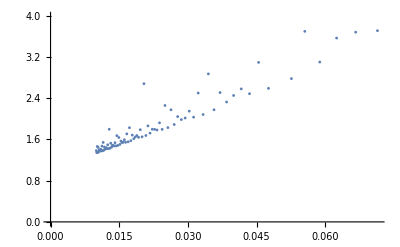

```mathematica
expList=Exponent[pSeries[[1]],z,List];
coefList=Coefficient[pSeries[[1]],z,#]&/@ expList;
theLCM=LCM@@(Denominator@expList);
 numerators=theLCM expList
rootTestTable=Table[
{1/numerators[[k]],N[1/(Abs[coefList[[k]]]^(4/numerators[[k]])),25]},
{k,15,Length@coefList}];
lp1=ListPlot[rootTestTable,PlotStyle->{PointSize[0.005]},AxesOrigin->{0,0}]
```

```mathematica
expList[[1;;10]]
LCM@@Denominator@expList[[1;;10]]
4 expList
```

{0,1/4,1/2,3/4,1,5/4,3/2,7/4,2,9/4}

4

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

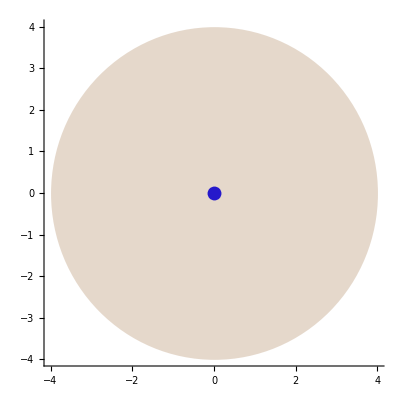
```mathematica
plot1=-Graphics-;
```

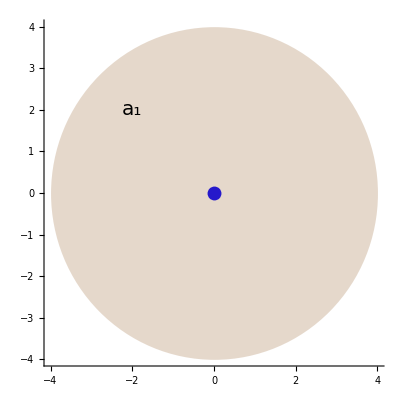

```mathematica
a1Text=Graphics@Text[Style["a_1",20,Black],{-2,2}];
Show[{plot1,a1Text}]
```

```mathematica
plot2=-Graphics-;
a1Textb=Graphics@Text[Style["a_1",20,Black],{-1/2,1/2}];
a2Textb=Graphics@Text[Style["a_2",20,Black],{-1.1,1}];
Show[{plot2,a1Textb,a2Textb}]
```

-Graphics-

### testCase0006: (z-1)(z+1)-w^2

```mathematica
$theFunction=w^2-(z-1)(z+1);
$theTestCase="testCase0006";
subDirectory=$theTestCase;

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;
f2[z_]:=Sqrt[(z-1)(z+1)]

pf2a=ParametricPlot3D[{Re@z,Im@z,Re@f2[z]}/.z->r Exp[I t],{r,0,3},{t,-Pi,Pi},PlotStyle->{Opacity[0.5],Blue}];
pf2b=ParametricPlot3D[{Re@z,Im@z,-Re@f2[z]}/.z->r Exp[I t],{r,0,3},{t,-Pi,Pi},PlotStyle->{Opacity[0.5],Red}];
Show[{pf2a,pf2b},PlotRange->All]
```

-Graphics3D-

```mathematica
f1[z_]:=Sqrt[z];
pf1=ParametricPlot3D[{Re@z,Im@z,Re@f1[z]}/.z->r Exp[I t],{r,0,3},{t,-Pi,Pi},PlotStyle->{Opacity[0.3],Blue},PlotRange->3];
pf2=ParametricPlot3D[{Re@z,Im@z,-Re@f1[z]}/.z->r Exp[I t],{r,0,3},{t,-Pi,Pi},PlotStyle->{Opacity[0.3],Red},PlotRange->3];

reContour=ParametricPlot3D[{Re@z,Im@z,Re@f1[z]}/.z->3/2 Exp[I t],{t,-Pi,Pi},PlotStyle->{Thickness[0.01],Yellow},PlotRange->3]
```

-Graphics3D-

```mathematica
Show[{pf1,pf2,reContour},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["Re[z]",14,Bold,Black],Style["Im[z]",14,Bold,Black],Style["Re(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted]]
```

-Graphics3D-

```mathematica
f1[z_]:=Sqrt[z];
imag1=ParametricPlot3D[{Re@z,Im@z,Im@f1[z]}/.z->r Exp[I t],{r,0,3},{t,-Pi,Pi},PlotStyle->{Opacity[0.3],Blue},PlotRange->3];
imag2=ParametricPlot3D[{Re@z,Im@z,-Im@f1[z]}/.z->r Exp[I t],{r,0,3},{t,-Pi,Pi},PlotStyle->{Opacity[0.3],Red},PlotRange->3];

imContour=ParametricPlot3D[{Re@z,Im@z,Im@f1[z]}/.z->3/2 Exp[I t],{t,Pi/6,2 Pi+Pi/2},PlotStyle->{Thickness[0.01],Yellow},PlotRange->3]
```

-Graphics3D-

```mathematica
theFunction=-z+w^2;
(*  start the contour at (1/2 Sqrt[1/2])*)
z0=3/2 Exp[Pi I/6];
w0=Sqrt[z0];
(* rotate around the branch sheets 4 Pi *)
tStart=Pi/6;
tEnd=tStart+4 Pi;
(*  create z(t) *)
Z[t_]:=3/2 Exp[I t];
(*  solve mIVP *)
wDeriv=w'[t]==((-(D[theFunction,z]/D[theFunction,w]) D[Z[t],t])/. {w->w[t],z->Z[t]});
imagSol=NDSolveValue[{wDeriv,w[tStart]==w0},w,{t,tStart,tEnd}];
(* create plot *)
imagContourPlot=ParametricPlot3D[{Re@z,Im@z,Im@imagSol[t]}/. z->Z[t],{t,tStart,tEnd},PlotStyle->{Thickness[0.01],Yellow}]
```

-Graphics3D-

```mathematica
zPoint=3/2 Exp[Pi I/6];
imagPoint3D=Graphics3D@{PointSize[0.02],Green,Point@{Re@zPoint,Im@zPoint,Im@f1[zPoint]}};
 Manipulate[
arrowArray=Table[{Re@z,Im@z,Im@f1[z]}/.z->3/2 Exp[t I],{t,tStart+0.1,tStop,(tStop-tStart)/50}];
defArrowG=Graphics3D@{Thickness[0.005],Arrow@arrowArray};
Show[{imag1,imag2,defArrowG,imagPoint3D},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["Re[z]",14,Bold,Black],Style["Im[z]",14,Bold,Black],Style["Re(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted]],
{{tStop,tStart+0.001},tStart+0.001,tEnd}
]
```

Table::iterb: Iterator {t,0.1+tStart,5.14866,1/50 (5.14866-tStart)} does not have appropriate bounds.

Show::gcomb: Could not combine the graphics objects in Show[{imag1,imag2,,imagPoint3D},AxesEdge→{{-1,-1},{1,-1},{-1,-1}},FaceGrids→{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel→{Re[z],Im[z],Re(w)},FaceGridsStyle→Directive[color,Dashing[{0,Small}]]].

Show::gcomb: Could not combine the graphics objects in ….

```mathematica
zPoint=3/2 Exp[Pi I/6];
imagPoint3D=Graphics3D@{PointSize[0.02],Green,Point@{Re@zPoint,Im@zPoint,Im@f1[zPoint]}};
 Manipulate[
imagArrowArray=Table[{Re@z,Im@z,Im@imagSol[t]}/.z->3/2 Exp[t I],{t,tStart+0.1,tStop,(tStop-tStart)/50}];
imagArrowG=Graphics3D@{Thickness[0.005],Arrow@imagArrowArray};
Show[{imag1,imag2,imagArrowG,imagPoint3D},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["Re[z]",14,Bold,Black],Style["Im[z]",14,Bold,Black],Style["Re(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted]],
{{tStop,tStart+0.001},tStart+0.001,tEnd}
]
```

Table::iterb: Iterator {t,0.1+tStart,4.77169,1/50 (4.77169-tStart)} does not have appropriate bounds.

Show::gcomb: Could not combine the graphics objects in Show[{imag1,imag2,,imagPoint3D},AxesEdge→{{-1,-1},{1,-1},{-1,-1}},FaceGrids→{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel→{Re[z],Im[z],Re(w)},FaceGridsStyle→Directive[color,Dashing[{0,Small}]]].

```mathematica
DynamicModule[{tStop=4.771694043251699},imagArrowArray=Table[{Re[z],Im[z],Im[imagSol[t]]}/.z->3/2 Exp[t ⅈ],{t,tStart+0.1,tStop,(tStop-tStart)/50}];imagArrowG=Graphics3D[{Thickness[0.005],Arrow[imagArrowArray]}];Show[{imag1,imag2,imagArrowG,imagPoint3D},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["Re[z]",14,Bold,Black],Style["Im[z]",14,Bold,Black],Style["Re(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted]]]
```

## Initialization

### aForm

```mathematica
(*evaluate the symbol to force autoloading*)Convert`TeX`ExpressionToTeX;

(*modify ExpressionToTeX so that it blocks $TeX to true*)
Unprotect[Convert`TeX`ExpressionToTeX];
Convert`TeX`ExpressionToTeX[expr_,o___?OptionQ]/;!TrueQ@$TeX:=Block[{$TeX=True},Convert`TeX`ExpressionToTeX[expr,o]]
Protect[Convert`TeX`ExpressionToTeX];

(*modify ordplus to reverse the order of polynomials*)
TraditionalFormDump`ordplus[x_,y_]/;$TeX:=Block[{$TeX=False},Reverse@TraditionalFormDump`ordplus[x,y]]

(*introduce the wrapper function ParameterVariableForm to allow one to specify what the*parameter variable is,that is,what variables are not the main polynomial variable*)
Options[ParameterVariableForm]={ParameterVariables->{}};

Unprotect[Times];
Times/:MakeBoxes[r_Rational s_,TraditionalForm]/;$TeX:=RowBox[{MakeBoxes[r,TraditionalForm],MakeBoxes[s,TraditionalForm]}]
Protect[Times];

ParameterVariableForm/:MakeBoxes[ParameterVariableForm[x_,opts:OptionsPattern[]],TraditionalForm]:=MakeBoxes[TraditionalForm[x,opts],TraditionalForm]

(*helper functions*)ClearAll[thecRules,toPowerBoxes,parenthesizeRow,coeffToBoxes,toMonomialBoxes];
thecRules[t_][poly_]:=Association@Sort@CoefficientRules[poly,{t}];
toPowerBoxes[t_]:=KeyMap[MakeBoxes[#]&[t^#]&@*First];
parenthesizeRow[boxes:{b:Except[_List]}]:=RowBox[{"(",b,")"}];
parenthesizeRow[boxes_]:=RowBox[{"(",RowBox@Flatten@boxes,")"}];coeffToBoxes//ClearAll;
(*first coeff is treated different*)
coeffToBoxes[assoc_]:=MapAt[MakeBoxes,1]@MapAt[{If[Negative[#],"-","+"],MakeBoxes[#]&@Abs@#}&,2;;]@assoc;
(*±1 are specials cases;no zero coeffs*)
toMonomialBoxes["1",coeff_]:=coeff;
toMonomialBoxes[power_,{sign_,coeff_}]:={sign,RowBox[{coeff," ",power}]};
toMonomialBoxes[power_,"1"]:=power;
toMonomialBoxes[power_,RowBox[{"-","1"}]]:=RowBox[{"-",power}];
toMonomialBoxes[power_,coeff_]:=RowBox[{coeff," ",power}];

aForm[f_]:=RawBoxes@RowBox@Riffle[#,"+"]&@KeyValueMap[toMonomialBoxes]@Map[parenthesizeRow]@Map[KeyValueMap[toMonomialBoxes]@*coeffToBoxes@*toPowerBoxes[z]@*thecRules[z]]@toPowerBoxes[w]@thecRules[w][f];

aForm2[f_]:=RawBoxes@RowBox@Riffle[#,"+"]&@KeyValueMap[toMonomialBoxes]@Map[parenthesizeRow]@Map[KeyValueMap[toMonomialBoxes]@*coeffToBoxes@*toPowerBoxes[c]@*thecRules[c]]@toPowerBoxes[z]@thecRules[z][f];
```